-UnitStep[-1+t]+UnitStep[t]

UnitStep[t]

(1/s-ⅇ^-s/s)/s

t-(-1+t) HeavisideTheta[-1+t]

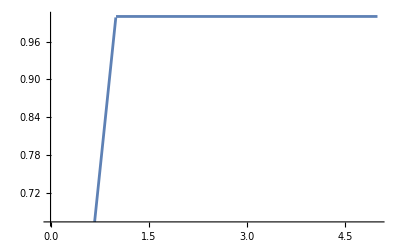

```mathematica
a = UnitStep[t]-UnitStep[t-1]
b = UnitStep[t]
c = LaplaceTransform[a,t,s]*LaplaceTransform[b,t,s]
d = InverseLaplaceTransform[c,s,t]
Plot[d,{t,0,5}]
```